```mathematica
k=100;Pr0=.72;Ra=10^5;R=Ra*Pr0;t0=1/100;a=0;
Ω=ImplicitRegion[0≤x≤1&&0≤y≤1,{x,y}];
UX[0][x_,y_]:=0;
VY[0][x_,y_]:=0;
Ρ[0][x_,y_]:=0;
TK[0][x_,y_]:=0;TX[0][x_,y_]:=0;
Do[
{UX[i],VY[i],Ρ[i],TK[i],TX[i]}=NDSolveValue[{{({{-μ,0},{0,-μ}}.u[x,y]{x,y}Inactive){x,y}Inactive+D[p[x,y],x]+UX[i-1][x,y]*D[u[x,y],x]+VY[i-1][x,y]*D[u[x,y],y]+(u[x,y]-UX[i-1][x,y])/t0-R*T[x,y]*Sin[a],({{-μ,0},{0,-μ}}.v[x,y]{x,y}Inactive){x,y}Inactive+D[p[x,y],y]+UX[i-1][x,y]*D[v[x,y],x]+VY[i-1][x,y]*D[v[x,y],y]-R*T[x,y]*Cos[a]+(v[x,y]-VY[i-1][x,y])/t0,D[u[x,y],x]+D[v[x,y],y]}=={0,0,0}/.μ->Pr0,{
DirichletCondition[{p[x,y]==0},y==1&&x==1],DirichletCondition[{u[x,y]==0,v[x,y]==0},y==0||y==1]},{UX[i-1][x,y]*D[T[x,y],x]+VY[i-1][x,y]*D[T[x,y],y]+(T[x,y]-TK[i-1][x,y])/t0-(D[T[x,y],x,x]+D[T[x,y],y,y])==NeumannValue[0,y==0||y==1],DirichletCondition[{u[x,y]==0,v[x,y]==0,T[x,y]==1},x==0],DirichletCondition[{u[x,y]==0,v[x,y]==0,T[x,y]==0},x==1]}},{u,v,p,T,Derivative[1,0][T]},{x,y}∈Ω,Method->{"FiniteElement","InterpolationOrder"->{u->2,v->2,p->1,T->2},"MeshOptions"->{"MaxCellMeasure"->0.0001}}],{i,1,k}];
```

```mathematica
MaximalBy[Table[{x,VY[k][x,.5]},{x,0,1,.0001}],Last]
```

{{0.066,68.7316}}

```mathematica
(*BenchmarkCase={x=0.066,vmax=68.59}*)
```

```mathematica
MaximalBy[Table[{y,UX[k][0.5,y]},{y,0,1,.0001}],Last]
```

{{0.8543,34.6607}}

```mathematica
(*BenchmarkCase={y=0.855,umax=34.73}*)
```

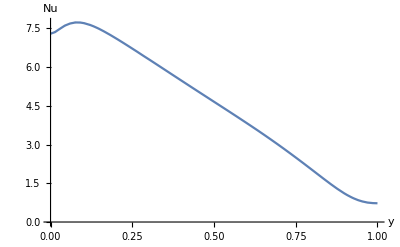
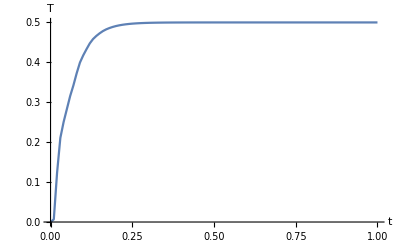

```mathematica
{Plot[-TX[k][0,y],{y,0,1},AxesLabel->{"y","Nu"}],ListLinePlot[Table[{i*t0,TK[i][0.5,.5]},{i,0,k}],AxesLabel->{"t","T"}]}
```

```mathematica
MaximalBy[Table[{y,-TX[k][0,y]},{y,0,1,0.0001}],Last]
```

{{0.0747,7.73417}}

```mathematica
(*BenchmarkCase={y=0.081,Numax=7.717}*)
```

```mathematica
NuAv=NIntegrate[UX[k][x,y]*TK[k][x,y]-TX[k][x,y],{x,0,1},{y,0,1},WorkingPrecision->5]
```

4.488

```mathematica
(*BenchmarkCase=4.519*)
```

```mathematica
Nu0=NIntegrate[-TX[k][0,y],{y,0,1},WorkingPrecision->5]
```

4.5274

```mathematica
(*BenchmarkCase=4.509*)
```

```mathematica
Nu05=NIntegrate[UX[k][.5,y]*TK[k][.5,y]-TX[k][0.5,y],{y,0,1},WorkingPrecision->5]
```

4.5252

```mathematica
(*BenchmarkCase=4.519*)

MinimalBy[Table[{y,-TX[k][0,y]},{y,0,1,0.0001}],Last]
```

{{1.,0.726786}}

```mathematica
(*BenchmarkCase={y=1,Numin=0.729}*)
```

```mathematica
(*Vahl Davis,G.de (1983):Natural convection of air in a square cavity:A bench mark numerical solution.Int.J.Numer.Methods Fluids 3,249–264*)
```

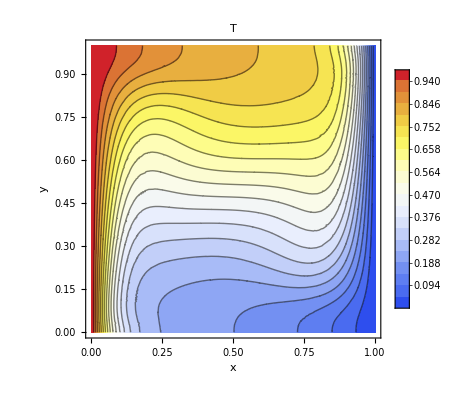
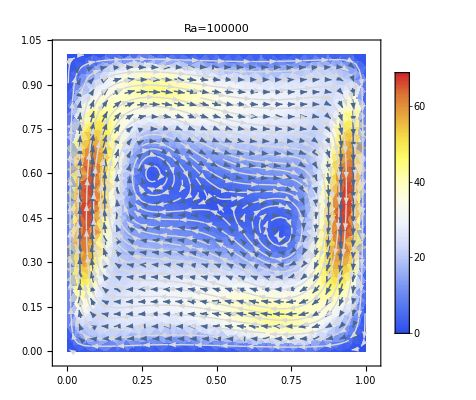

```mathematica
{ContourPlot[TK[k][x,y],{x,y}∈Ω,PlotLegends->Automatic,Contours->20,PlotPoints->25,ColorFunction->"TemperatureMap",AxesLabel->{"x","y"},PlotLabel->T],StreamDensityPlot[{UX[k][x,y],VY[k][x,y]},{x,y}∈Ω,StreamPoints->Fine,StreamStyle->LightGray,PlotLegends->Automatic,VectorPoints->Fine,ColorFunction->"TemperatureMap",PlotLabel->Row[{"Ra=",Ra}]]}
```